## Primos e grafos: uma pesquisa sobre divisores

Um número primo é um número natural maior do que 1 que possui apenas dois divisores: o número 1 e ele próprio.

```mathematica
Table[Prime[x],{x,50}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229}

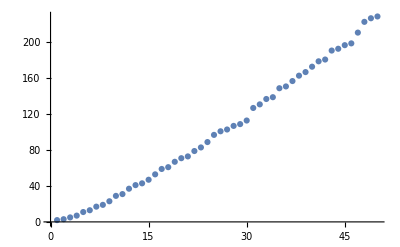

```mathematica
ListPlot[Table[Prime[x],{x,50}]]
```

Aqui, define-se um d-primo como um número natural que tem exatamente d-divisores. Usando essa definição, é evidente que os números primos são o caso particular d = 2.

```mathematica
dprimes=GroupBy[Range[100], Length@Divisors[#]&]//KeySort;
```

```mathematica
TableForm[Values@dprimes, TableHeadings->{Keys@dprimes, None}]
```

1 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2 | 2 | 3 | 5 | 7 | 11 | 13 | 17 | 19 | 23 | 29 | 31 | 37 | 41 | 43 | 47 | 53 | 59 | 61 | 67 | 71 | 73 | 79 | 83 | 89 | 97 |  |  |  |  |  |  | 
3 | 4 | 9 | 25 | 49 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
4 | 6 | 8 | 10 | 14 | 15 | 21 | 22 | 26 | 27 | 33 | 34 | 35 | 38 | 39 | 46 | 51 | 55 | 57 | 58 | 62 | 65 | 69 | 74 | 77 | 82 | 85 | 86 | 87 | 91 | 93 | 94 | 95
5 | 16 | 81 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
6 | 12 | 18 | 20 | 28 | 32 | 44 | 45 | 50 | 52 | 63 | 68 | 75 | 76 | 92 | 98 | 99 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
7 | 64 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
8 | 24 | 30 | 40 | 42 | 54 | 56 | 66 | 70 | 78 | 88 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
9 | 36 | 100 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
10 | 48 | 80 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
12 | 60 | 72 | 84 | 90 | 96 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

Se dividirmos ambos lados por x, temos a densidade de primos.

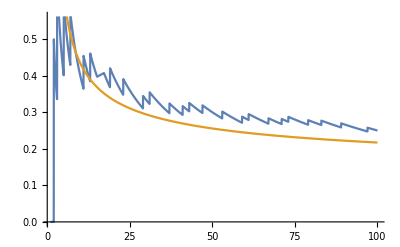

```mathematica
Plot[{PrimePi[x]/x,1/Log[x]},{x,1,100}]
```

```mathematica
primes=GroupBy[Range[10000], Length@Divisors[#]&]//KeySort;
```

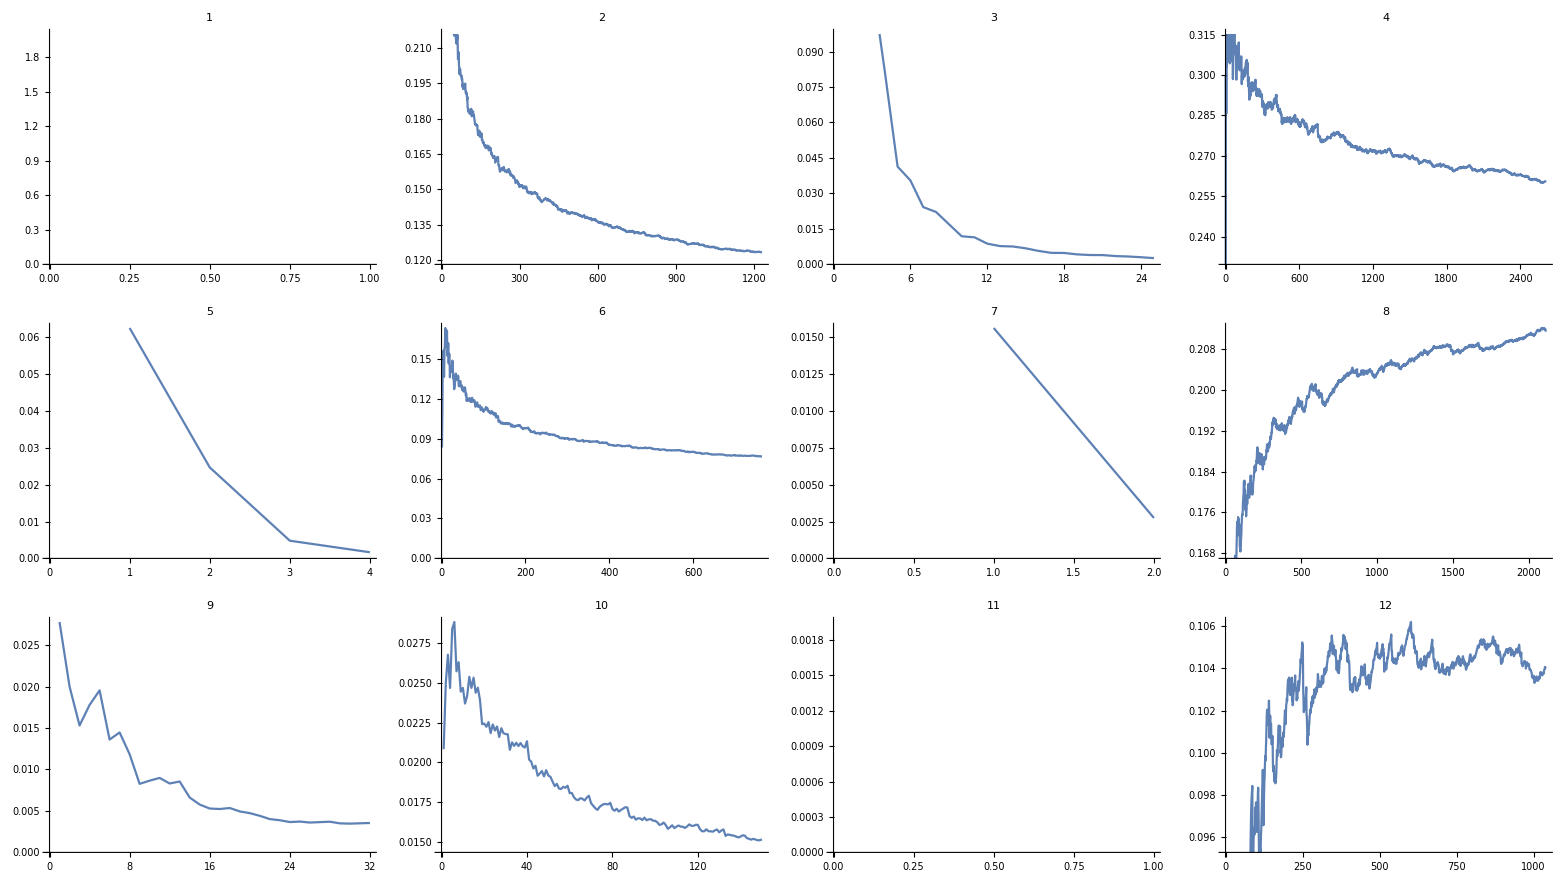

```mathematica
Partition[Table[ListLinePlot[Table[x/primes[n][[x]],{x, Length[primes[n]]}],PlotLabel->n], {n,12}],4]//Grid
```

## Lacunas

As lacunas entre primos sucessivos tambem eh muito estudada pelos matematicos.

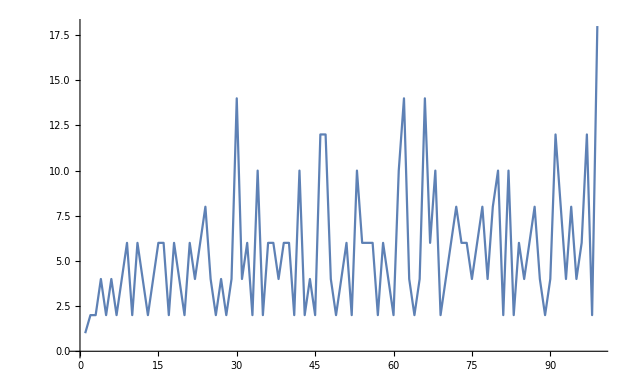

```mathematica
ListLinePlot[Differences@Table[Prime[x],{x,100}]]
```

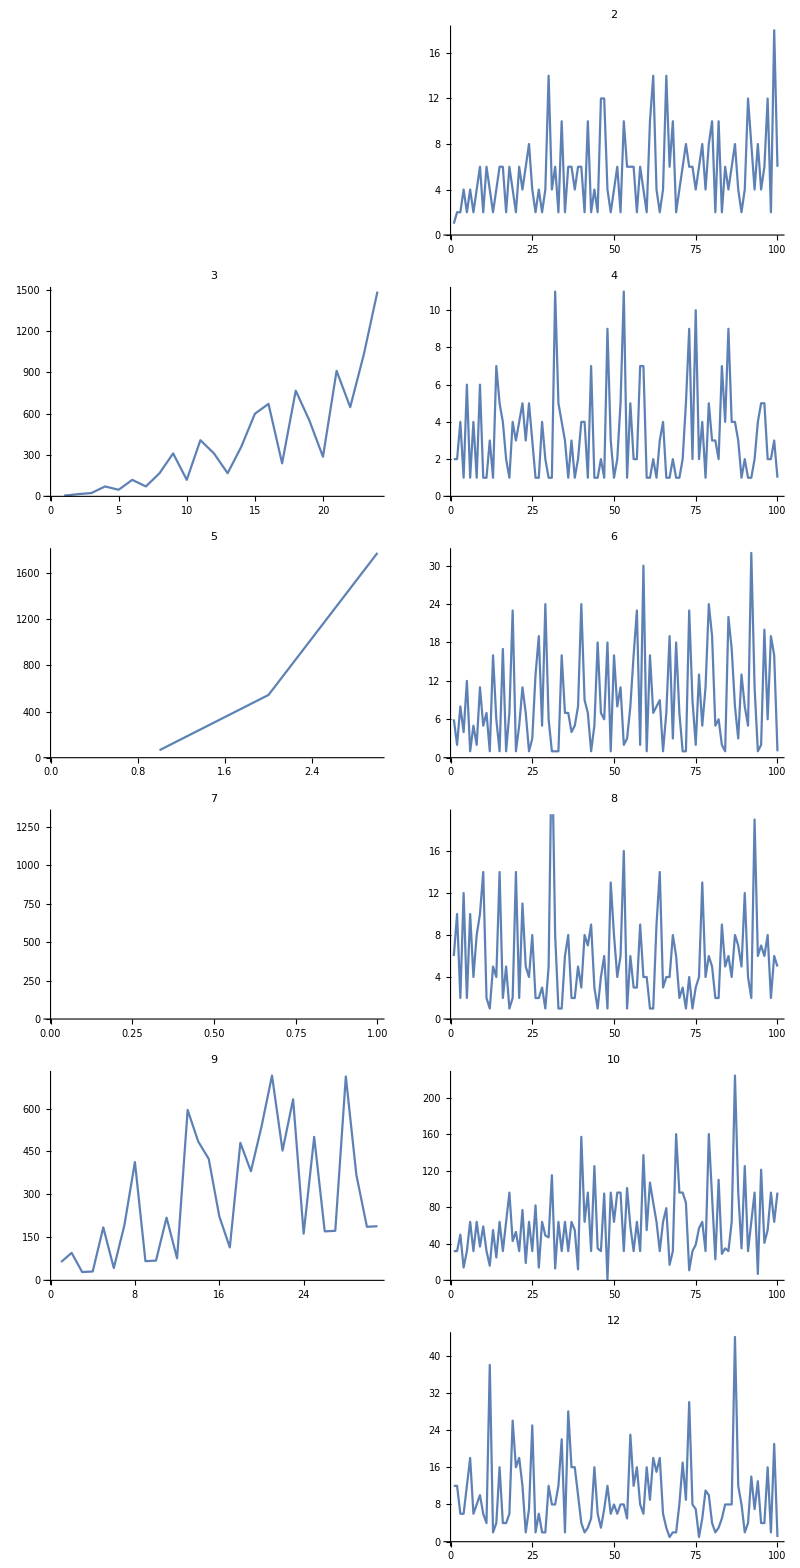

```mathematica
Partition[Table[ListLinePlot[Take[Table[primes[n][[x+1]]-primes[n][[x]],{x, Length[primes[n]]-1}],UpTo[100]],PlotLabel->n,ImageSize->Medium], {n,12}],2]//Grid
```

```mathematica
Partition[Table[ResourceFunction["SequenceGraph"][Take[Table[primes[n][[x+1]]-primes[n][[x]],{x, Length[primes[n]]-1}],UpTo[100]],PlotLabel->n,ImageSize->Medium], {n,12}],2]//Grid
```

-Graphics-

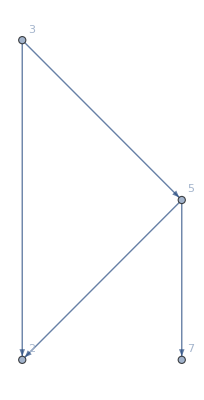
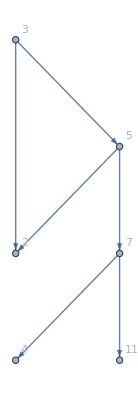
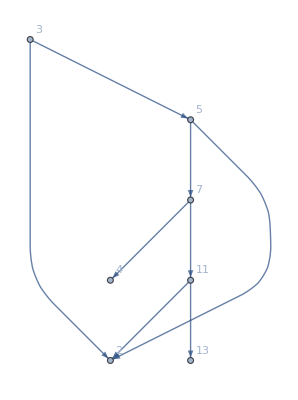
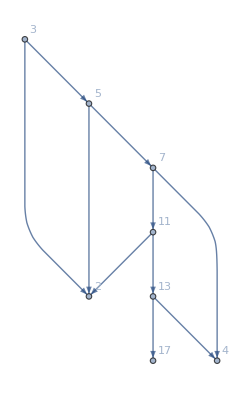
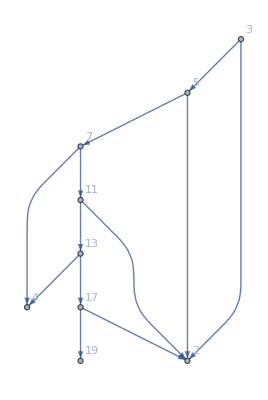
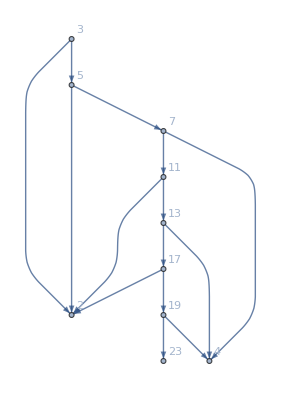
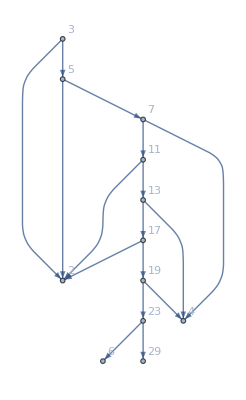
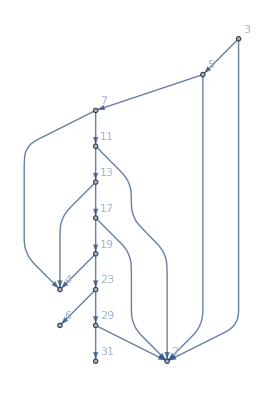

```mathematica
t=Table[Nest[Differences,allPrimes[[2,2;;100]],n],{n,0,8}];
cons=Table[Flatten@Table[{t[[1,x]]->t[[1,x+1]]-t[[1,x]],t[[1,x]]->t[[1,x+1]]},{x,y}],{y,2,30}];
Table[Graph[Union[s,s],VertexLabels->"Name"],{s,cons}]
```

## Natural Visibility

More formally, we can establish the following visibility criteria : two arbitrary data values (t_a, y_a) and (t_b, y_b) will have visibility, and consequently will become two connected nodes of the associated graph, if any other data (t_c, y_c) placed between them fulfills:
-Graphics-

```mathematica
visibleQ[a_Integer, b_Integer, ts_List]:=Catch[
	Do[
		If[Not[ts[[x,2]] < ts[[b,2]] + (ts[[a,2]] − ts[[b,2]])(ts[[b,1]]−ts[[x,1]])/(ts[[b,1]]−ts[[a,1]])],Throw[False]],
		{x,a+1,b-1}
	];
	Throw[True]
]
```

```mathematica
naturalVisibility[series_]:=Block[{visibles},
	visibles={};
	Do[
		Do[
			If[visibleQ[i,j,series],AppendTo[visibles,i->j],Null],
			{j,i+1,Length@series}
		],
		{i,1,Length@series-1}
	];
	Return[visibles]
]
```

```mathematica
nv=naturalVisibilityLinks[Table[{x,primes[2][[x+1]]-primes[2][[x]]},{x,100}]];
```

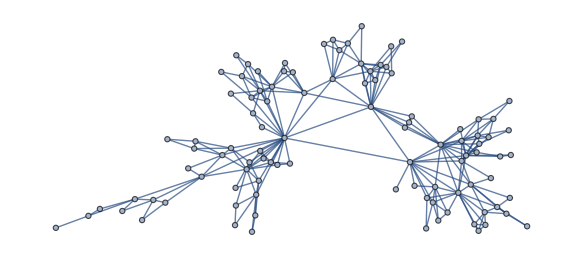

```mathematica
naturalGraph=Graph[nv, DirectedEdges->False, VertexLabelStyle-> Large]
```

```mathematica
VertexDegree[naturalGraph]//Counts//KeySort//Values
```

{2,25,10,21,12,7,5,2,5,3,2,1,1,1,1,1,1}

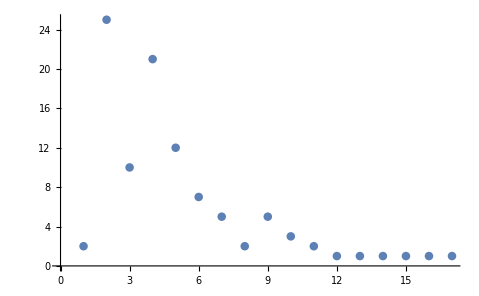

```mathematica
ListPlot[VertexDegree[naturalGraph]//Counts//KeySort//Values]
```

## Horizontal Visibility

x_i,x_j>x_n for all n such that  i<n<j.

```mathematica
horizontalQ[a_Integer, b_Integer, ts_List]:=Catch[
	Do[
		If[Not[ts[[x,2]] < ts[[a,2]] && ts[[x,2]] < ts[[b,2]]],Throw[False]],
		{x,a+1,b-1}
	];
	Throw[True]
]
```

```mathematica
horizontalVisibilityLinks[vals_List]:=Block[{visibles},
visibles={};Do[
Do[
If[horizontalQ[i,j,vals],AppendTo[visibles,i->j],Null],
{j,i+1,Length@vals}
],
{i,1,Length@vals-1}];
visibles
]
```

```mathematica
hv=horizontalVisibilityLinks[Table[{x,primes[2][[x+1]]-primes[2][[x]]},{x,1000}]];
```

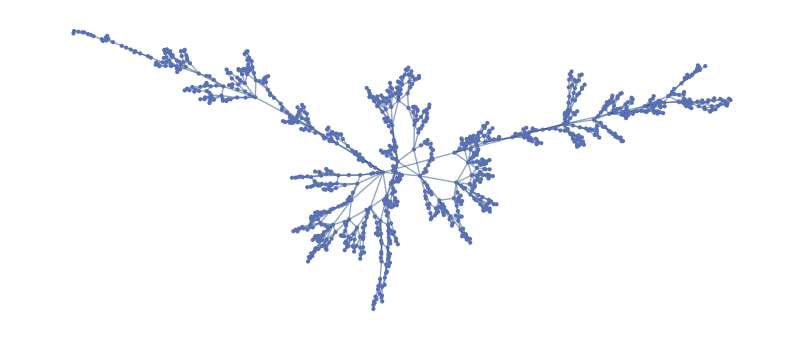

```mathematica
horizontalGraph=Graph[hv, DirectedEdges->False, VertexLabelStyle-> Large]
```

```mathematica
VertexDegree[horizontalGraph]//Counts//KeySort//Values
```

{2,374,263,143,99,36,35,17,13,4,7,4,3}

```mathematica
ListPlot[VertexDegree[naturalGraph]//Counts//KeySort//Values]
```

-Graphics-

```mathematica
Length/@primes
```

<|1→1,2→1229,3→25,4→2608,5→4,6→764,7→2,8→2114,9→32,10→150,11→1,12→1040,13→1,14→41,15→15,16→800,18→159,20→157,21→5,22→3,24→449,25→2,27→7,28→30,30→44,32→130,33→1,35→1,36→80,40→36,42→7,45→3,48→45,50→2,54→4,56→2,60→4,64→2|>

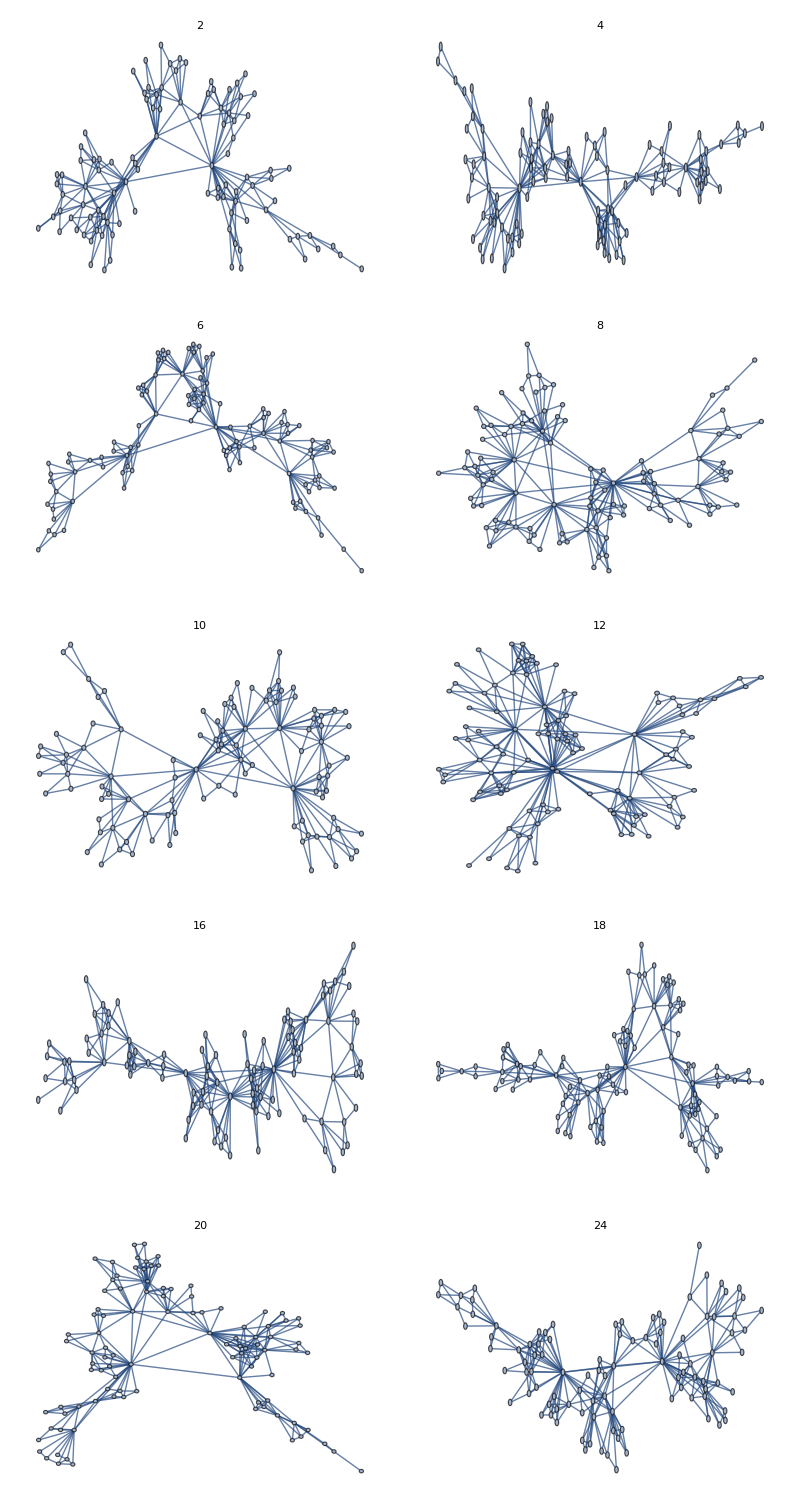

```mathematica
Partition[Table[
Graph[naturalVisibilityLinks[Table[{x,primes[n][[x+1]]-primes[n][[x]]},{x,100}]],DirectedEdges->False, VertexLabelStyle-> Large,PlotLabel->n], {n,{2,4,6,8,10,12,16,18,20,24}}],2]//Grid
```

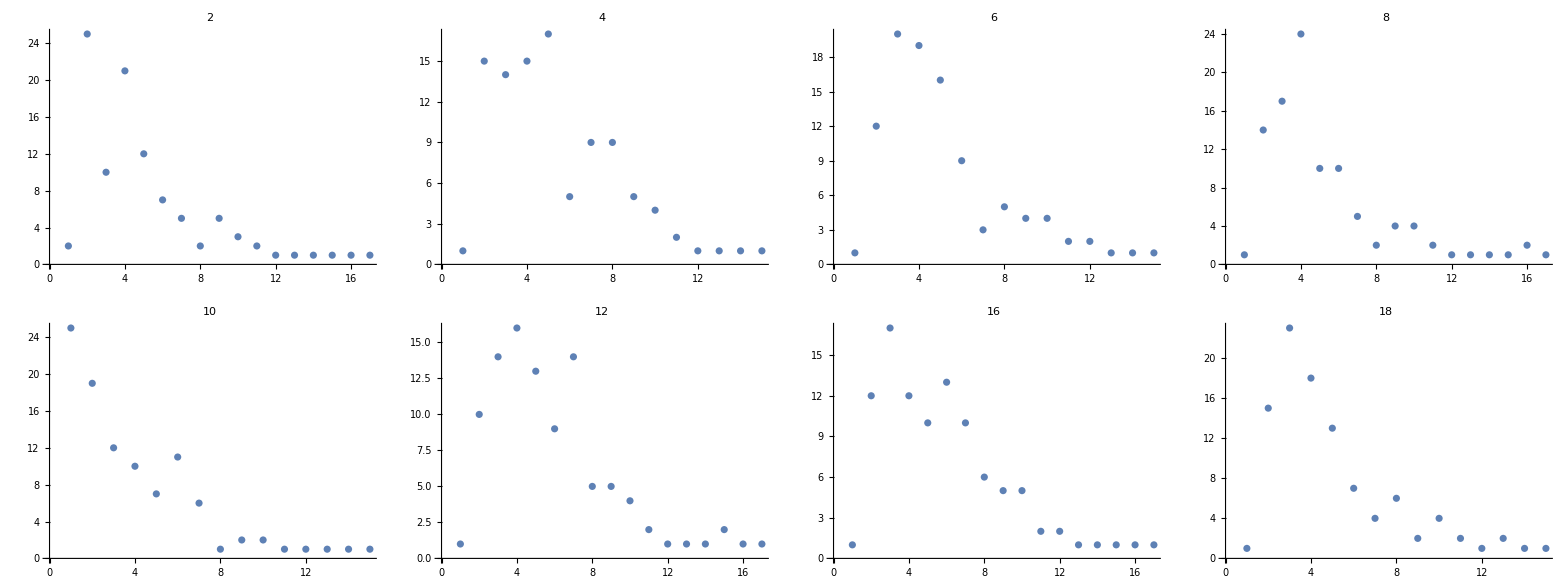

```mathematica
Partition[Table[
ListPlot[VertexDegree[Graph[naturalVisibilityLinks[Table[{x,primes[n][[x+1]]-primes[n][[x]]},{x,100}]],DirectedEdges->False]]//Counts//KeySort//Values,PlotLabel->n],{n,{2,4,6,8,10,12,16,18}}],4]//Grid
```